Raphael Reitzig, 2014 -- MIT License

```mathematica
(* Some auxiliary functions *)
SumList[l_]:=Fold[#1+#2&,0,l];
ProdList[l_]:=Fold[#1*#2&,1,l];
AndList[l_]:=Fold[#1&&#2&,True,l];
LargerIndices[l1_,l2_]:=Flatten[MapIndexed[If[#1-l2[[#2[[1]]]]>0 ,{#2}[[1]],{}]&,l1]];
SmallerIndices[l1_,l2_]:=LargerIndices[l2,l1];
AbsListDist[l1_,l2_]:=SumList[Abs[l1-l2]];
```

```mathematica
Needs["GeneralUtilities`"];
ExpectedSteps[p_]:=ExpectedSteps[p]=Where[
n=Length[p],
elements=Table[i,{i,1,n}],
(* Create state set: all Parikh vectors with sum ≤n minis
absorbing state (1,...,1) *)
tstates=Select[Tuples[{0}~Join~elements,n],SumList[#]≤n&&ProdList[#]≠1&],
first=tstates[[1]], (* Check that first state is (0,...,0) *)

(* From here, we follow 
	[en.wiki]/Absorbing_Markov_chain#Fundamental_matrix *)
t=Length[tstates],
q=Table[Table[Where[
si=tstates[[i]],
sj=tstates[[j]],
larger=LargerIndices[sj, si],
smaller=SmallerIndices[sj, si],
dist=AbsListDist[si,sj],
	If[SumList[si]<n,
		(* First n-1 steps *)
		If[Length[smaller]==0&& Length[larger]==1&&dist==1,
		(* Have a vector with proper distance *)
		p[[larger[[1]]]],
		(* No way to get there *)
		0],
		(* Later *)
		If[i==j,
		(* Same state: sum over non-zero components *)
		SumList[MapIndexed[#/n*p[[#2[[1]]]]&,si]],
		(* Different state: at most one way to get there *)
		If[Length[smaller]==1&& Length[larger]==1&&dist==2,
		(* Have a vector with proper distance *)
		si[[smaller[[1]]]]/n*p[[larger[[1]]]],
		(* No way to get there *)
		0]
		]
	]
],{j,1,t}],{i,1,t}],
f=Inverse[IdentityMatrix[t]-q],
(f.Table[1,{i,1,t}])[[1]]//Simplify]
```

```mathematica
e3=ExpectedSteps[{q1,q2,1-q1-q2}];
Plot3D[e3,{q1,0,1},{q2,0,1},RegionFunction->Function[{q1,q2},q1+q2<1]]
```

-Graphics3D-

```mathematica
e4=ExpectedSteps[{q1,q2,q3,1-q1-q2-q3}]
```

$Aborted

n | 2 | 3 | 4 | 5 | 6
E | 3 | 8 | 17 | 38 | 88

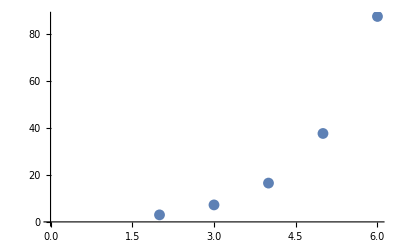

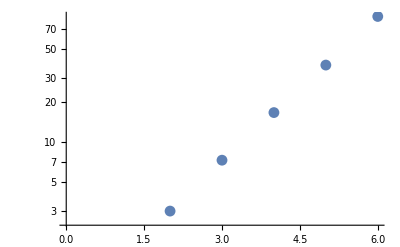

```mathematica
max=6;
t=Table[{n,N@ExpectedSteps[Table[1/n,{i,1,n}]]},{n,2,max}];
TableForm[Ceiling[t]//Transpose,TableHeadings->{{"n","E"}}]
ListPlot[t,PlotRange->{{0,max},All}]
ListLogPlot[t,PlotRange->{{0,max},All}]
```